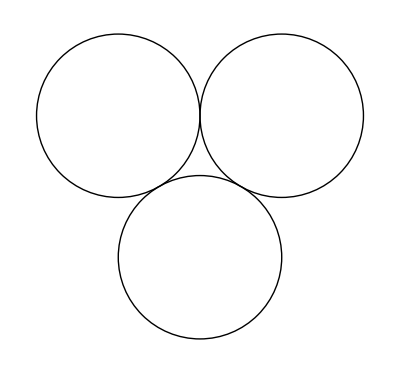

```mathematica
n = 5;
R= 10;
r = Sqrt[3]/(2+Sqrt[3])*R;

DrawCircles[{x_,y_,R_}]:=
Module[
{r= Sqrt[3]/(2+Sqrt[3])*R},
Graphics[{
Circle[{x,y-R+r},r],
Circle[{x+(R-r)*Cos[Pi/6],y+(R-r)*Sin[Pi/6]},r],
Circle[{x+(R-r)*Cos[5Pi/6],y+(R-r)*Sin[5Pi/6]},r]
} ]
]
DrawCircles[{0,0,R}]
```

```mathematica
Coords={{0,0,10}}
CoordsSearch[x_,y_,R_,n_]:=
Module[
{r= Sqrt[3]/(2+Sqrt[3])*R},
Coords = Insert[Coords,{x,y-R+r,r},-1];
If[n<5,CoordsSearch[x,y-R+r,r,n+1], Nothing];
Coords = Insert[Coords,{x+(R-r)*Cos[Pi/6],y+(R-r)*Sin[Pi/6],r},-1];
If[n<5,CoordsSearch[x+(R-r)*Cos[Pi/6],y+(R-r)*Sin[Pi/6],r,n+1], Nothing];
Coords = Insert[Coords,{x+(R-r)*Cos[5Pi/6],y+(R-r)*Sin[5Pi/6],r},-1];
If[n<5,CoordsSearch[x+(R-r)*Cos[5Pi/6],y+(R-r)*Sin[5Pi/6],r,n+1], Nothing];
]
```

{{0,0,10}}

```mathematica
CoordsSearch[0,0,10,0]
```

{{0,0,10},{0,-10+(10 √3)/(2+√3),(10 √3)/(2+√3)},{0,-10+30/(2+√3)^2,30/(2+√3)^2},{0,-10+(30 √3)/(2+√3)^3,(30 √3)/(2+√3)^3},{0,-10+90/(2+√3)^4,90/(2+√3)^4},{0,-10+(90 √3)/(2+√3)^5,(90 √3)/(2+√3)^5},{0,-10+270/(2+√3)^6,270/(2+√3)^6},{1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{-1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{-1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{1/2 √3 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),-10+(30 √3)/(2+√3)^3+1/2 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),90/(2+√3)^4},{-1/2 √3 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),-10+(30 √3)/(2+√3)^3+1/2 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),90/(2+√3)^4},{1/2 √3 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),-10+30/(2+√3)^2+1/2 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),(30 √3)/(2+√3)^3},{-1/2 √3 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),-10+30/(2+√3)^2+1/2 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),(30 √3)/(2+√3)^3},{1/2 √3 (-30/(2+√3)^2+(10 √3)/(2+√3)),-10+(10 √3)/(2+√3)+1/2 (-30/(2+√3)^2+(10 √3)/(2+√3)),30/(2+√3)^2},{-1/2 √3 (-30/(2+√3)^2+(10 √3)/(2+√3)),-10+(10 √3)/(2+√3)+1/2 (-30/(2+√3)^2+(10 √3)/(2+√3)),30/(2+√3)^2},{1/2 √3 (10-(10 √3)/(2+√3)),1/2 (10-(10 √3)/(2+√3)),(10 √3)/(2+√3)},{-1/2 √3 (10-(10 √3)/(2+√3)),1/2 (10-(10 √3)/(2+√3)),(10 √3)/(2+√3)}}

{{0,0,10},{0,-10+(10 √3)/(2+√3),(10 √3)/(2+√3)},{0,-10+30/(2+√3)^2,30/(2+√3)^2},{0,-10+(30 √3)/(2+√3)^3,(30 √3)/(2+√3)^3},{0,-10+90/(2+√3)^4,90/(2+√3)^4},{0,-10+(90 √3)/(2+√3)^5,(90 √3)/(2+√3)^5},{0,-10+270/(2+√3)^6,270/(2+√3)^6},{1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{-1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{-1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{1/2 √3 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),-10+(30 √3)/(2+√3)^3+1/2 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),90/(2+√3)^4},{-1/2 √3 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),-10+(30 √3)/(2+√3)^3+1/2 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),90/(2+√3)^4},{1/2 √3 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),-10+30/(2+√3)^2+1/2 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),(30 √3)/(2+√3)^3},{-1/2 √3 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),-10+30/(2+√3)^2+1/2 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),(30 √3)/(2+√3)^3},{1/2 √3 (-30/(2+√3)^2+(10 √3)/(2+√3)),-10+(10 √3)/(2+√3)+1/2 (-30/(2+√3)^2+(10 √3)/(2+√3)),30/(2+√3)^2},{-1/2 √3 (-30/(2+√3)^2+(10 √3)/(2+√3)),-10+(10 √3)/(2+√3)+1/2 (-30/(2+√3)^2+(10 √3)/(2+√3)),30/(2+√3)^2}}

{{0,0,10},{0,-10+(10 √3)/(2+√3),(10 √3)/(2+√3)},{0,-10+30/(2+√3)^2,30/(2+√3)^2},{0,-10+(30 √3)/(2+√3)^3,(30 √3)/(2+√3)^3},{0,-10+90/(2+√3)^4,90/(2+√3)^4},{0,-10+(90 √3)/(2+√3)^5,(90 √3)/(2+√3)^5},{0,-10+270/(2+√3)^6,270/(2+√3)^6},{1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{-1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{-1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{1/2 √3 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),-10+(30 √3)/(2+√3)^3+1/2 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),90/(2+√3)^4},{-1/2 √3 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),-10+(30 √3)/(2+√3)^3+1/2 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),90/(2+√3)^4},{1/2 √3 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),-10+30/(2+√3)^2+1/2 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),(30 √3)/(2+√3)^3},{-1/2 √3 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),-10+30/(2+√3)^2+1/2 (-(30 √3)/(2+√3)^3+30/(2+√3)^2),(30 √3)/(2+√3)^3}}

{{0,0,10},{0,-10+(10 √3)/(2+√3),(10 √3)/(2+√3)},{0,-10+30/(2+√3)^2,30/(2+√3)^2},{0,-10+(30 √3)/(2+√3)^3,(30 √3)/(2+√3)^3},{0,-10+90/(2+√3)^4,90/(2+√3)^4},{0,-10+(90 √3)/(2+√3)^5,(90 √3)/(2+√3)^5},{0,-10+270/(2+√3)^6,270/(2+√3)^6},{1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{-1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{-1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{1/2 √3 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),-10+(30 √3)/(2+√3)^3+1/2 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),90/(2+√3)^4},{-1/2 √3 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),-10+(30 √3)/(2+√3)^3+1/2 (-90/(2+√3)^4+(30 √3)/(2+√3)^3),90/(2+√3)^4}}

{{0,0,10},{0,-10+(10 √3)/(2+√3),(10 √3)/(2+√3)},{0,-10+30/(2+√3)^2,30/(2+√3)^2},{0,-10+(30 √3)/(2+√3)^3,(30 √3)/(2+√3)^3},{0,-10+90/(2+√3)^4,90/(2+√3)^4},{0,-10+(90 √3)/(2+√3)^5,(90 √3)/(2+√3)^5},{0,-10+270/(2+√3)^6,270/(2+√3)^6},{1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{-1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5},{-1/2 √3 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),-10+90/(2+√3)^4+1/2 (-(90 √3)/(2+√3)^5+90/(2+√3)^4),(90 √3)/(2+√3)^5}}

{{0,0,10},{0,-10+(10 √3)/(2+√3),(10 √3)/(2+√3)},{0,-10+30/(2+√3)^2,30/(2+√3)^2},{0,-10+(30 √3)/(2+√3)^3,(30 √3)/(2+√3)^3},{0,-10+90/(2+√3)^4,90/(2+√3)^4},{0,-10+(90 √3)/(2+√3)^5,(90 √3)/(2+√3)^5},{0,-10+270/(2+√3)^6,270/(2+√3)^6},{1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6},{-1/2 √3 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),-10+(90 √3)/(2+√3)^5+1/2 (-270/(2+√3)^6+(90 √3)/(2+√3)^5),270/(2+√3)^6}}

{{0,0,10},{0,-10+(10 √3)/(2+√3),(10 √3)/(2+√3)},{1/2 √3 (10-(10 √3)/(2+√3)),1/2 (10-(10 √3)/(2+√3)),(10 √3)/(2+√3)},{-1/2 √3 (10-(10 √3)/(2+√3)),1/2 (10-(10 √3)/(2+√3)),(10 √3)/(2+√3)}}

{{0,-10+(10 √3)/(2+√3),(10 √3)/(2+√3)},{1/2 √3 (10-(10 √3)/(2+√3)),1/2 (10-(10 √3)/(2+√3)),(10 √3)/(2+√3)},{-1/2 √3 (10-(10 √3)/(2+√3)),1/2 (10-(10 √3)/(2+√3)),(10 √3)/(2+√3)}}

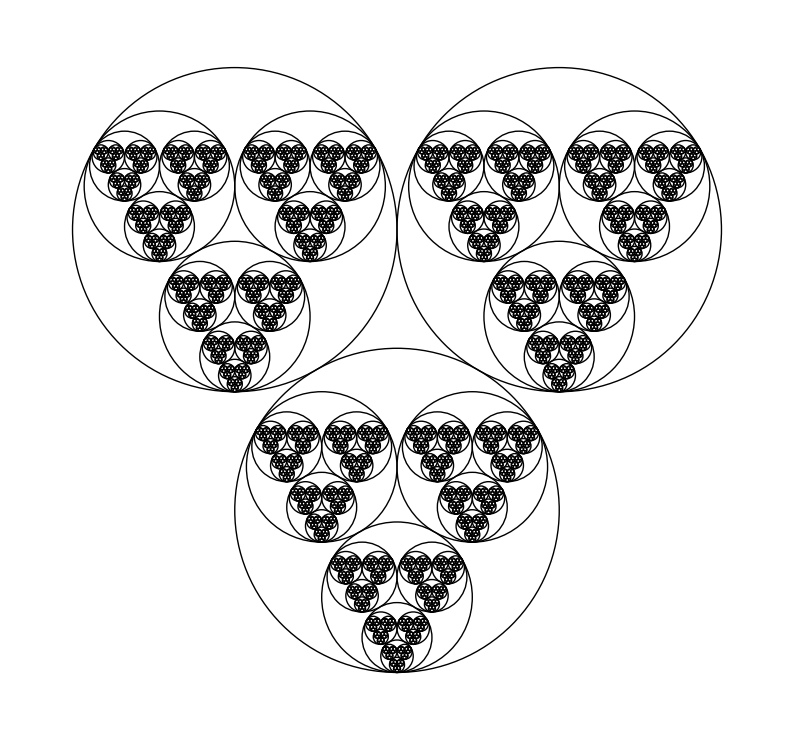

```mathematica
Show[Map[DrawCircles,Coords]]
```

```mathematica
Length[Coords]
```

1093